```mathematica
Clear["Global`*"]
<<qfold.mx
<<qneck.mx
<<linerfold.mx
<<linerneck.mx
<<qfletcher.mx
<<qfletcherneck.mx
$Assumptions = p>0&&r>0&&n0>1&&n1>1&&Q>0&&u>0;
qfletcher[p_, r_, n0_, n1_] = Simplify[q[p, r, n0, Q]/.Q->Sqrt[n0/n1]*r];
fold[λ_, r_, n0_, n1_,u_] = Simplify[1 - qfold[2π/λ, r, n0, n1, u]];
neck[λ_, r_, n0_, n1_,u_] = Simplify[-1 + qneck[2π/λ, r, n0, n1, u]];
liner[λ_, r_, u_] = Simplify[1-linerfold[2π/λ, r, u]];
fletcher[λ_, r_, n0_, n1_] = Simplify[1- qfletcher[2π/λ, r, n0, n1]];
fletcherneck[λ_, r_, n0_, n1_] = Simplify[-1+ qfletcherneck[2π/λ, r, n0, Sqrt[n0/n1]r]];
```

```mathematica
folder =""; (*Input your working FOLDER*)
Clear[plots];
plots = {}; j=1;
Manipulate[plt = LogLinearPlot[fold[λ,r,n0,n1,u], {λ, 0.5, 1000},PlotStyle->{Thick,ColorData[63,"ColorList"][[j]]}, ImageSize->500,Frame->{True,True,False,False},FrameLabel->{Style["λ/H",Orange,FontSize->13],Style["(-1+q)sgn(D_xx)",Purple,FontSize->14]},AspectRatio->1, PlotRange->All, RotateLabel->True, PlotLabels->Placed[Style["n_0="<>ToString[Round[n0]]<>" n_1="<>ToString[Round[n1]]<>"\n r="<>ToString[r]<>" u="<>ToString[u],FontSize->10], Above]],
Button["Export",Export[folder<>"\\Finite\\"<>ToString[Round[n0]]<>"."<>ToString[Round[n1]]<>"."<>ToString[u]<>".png",plt]],{plt,ControlType->None},
{n0, 1.001, 10.01, 1, Appearance->"Labeled"}, {n1, 1.001, 10.01, 1, Appearance->"Labeled"}, {{r,0.01},0.001,1,0.0001,Appearance->"Labeled"},
{{u, 100}, 10, 0, 1, Row@{Manipulator[Dynamic[Log[2, #1],(u=2^#1)&],  #2]," ",InputField[Dynamic@u]}&},
Button["Add Plot", AppendTo[plots, {r, n0, n1, u}]; j+=1;]]
```

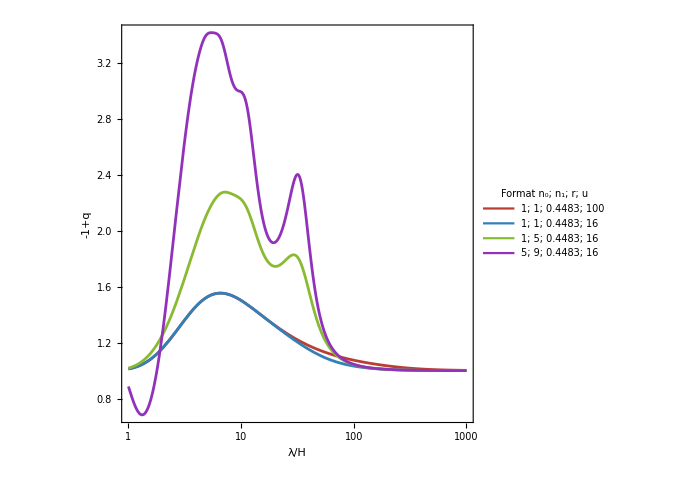

```mathematica
(*Draw all plots previously added*)
plt = LogLinearPlot[Evaluate[fold[λ,#1,#2,#3, #4] & [Sequence@@#]&/@plots], {λ, 1, 1000},PlotStyle->ColorData[63,"ColorList"][[1;;Length[plots]]],ImageSize->500,Frame->{True,True,False,False},FrameLabel->{Style["λ/H",Orange,FontSize->13],Style["-1+q",Purple,FontSize->14]},AspectRatio->1, PlotRange->All, RotateLabel->False,
PlotLegends->LineLegend[ColorData[63,"ColorList"][[;;Length[plots]]],ToString[Round[#2]]<>"; "<>ToString[Round[#3]]<>"; "<>ToString[#1]<>"; "<>ToString[#4]&[Sequence@@#]&/@plots, LegendLabel->"Format n_0; n_1; r; u"]]
```